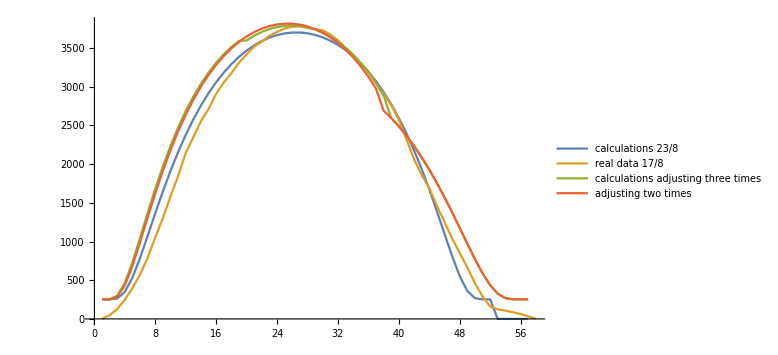

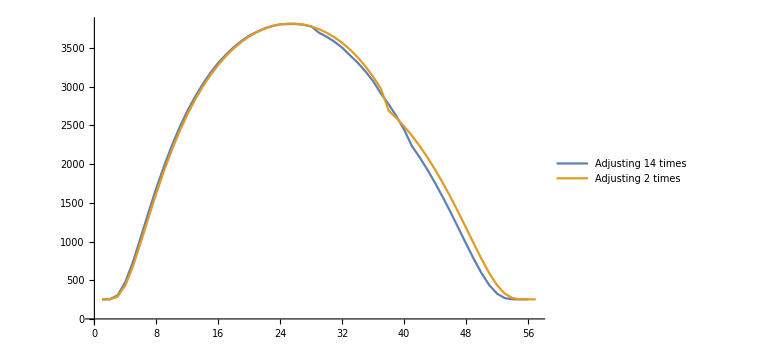

```mathematica
(* again calculations, but now with real data as power loss function *)
(* given a day, feed corresponding data, check if length is same as sunPositions, scale expected output maybe 
candidates: 13/5, 19/7, 17/8

todo: automatically search best time to set angle 2nd time, compare with one time and also with ten times to see if more (like three) would help or not
*)

year = 2016;

(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[i_?NumericQ,a_?NumericQ,d_]:= ( (* params: index of sunPositions table, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = sunPositions[[i]]; (* lookup sun position *)

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = -22 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)

(* parameters for clear day *)
directPowerClear[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

(* parameters from urban visibility haze model *)
directPower[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

(* http://www.solarpaneltilt.com/ *)
(*directPowerWeb[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
If[theta>Pi/2,
0,
1.35*(1/1.35)^(Sec[theta])*1000
]
)*)

calculatesunPos[d_] := (
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,d];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,d];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[d,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,25} 
];
)

(* misalignment over day *)
(*ListPlot[Table[
angle[i,25,DateObject[{2016,8,17}]]
,{i,1,Length[sunPositions]}
]]*)

(* sun insolation over day, 26.4 m2 panels *)
(*ListPlot[Table[
directPower[i,25,DateObject[{2016,8,17}]]*26.4
,{i,1,Length[sunPositions]}
]]*)
(* data adapted to from sunrise, 6:33, to sunset, 21:00. Length of sunPositions and data are both 58 *)
(* day = DateObject[{2016,8,17}]; *)
dataAugust = {0,47.5,128.167,247.833,398.167,574.333,789,1053.83,1304.83,1584.33,1846.17,2144,2348.33,2555.83,2712,2908.67,3055.33,3176.33,3310.33,3419.17,3519.17,3580.67,3659.33,3707.17,3753.17,3775.17,3781,3759.5,3746.17,3728.5,3675,3599.67,3504.67,3411.83,3302.83,3197.33,3046.5,2912.83,2761.17,2574.83,2324.33,2062.5,1862.17,1688.83,1465,1254,1041.5,853.167,666,463,291.833,160.667,124.333,106.833,86,62.8333,33.3333,2};
(* day = DateObject[{2016,5,13}]; *)
dataMay = {0,19.5,57,118.667,200.833,278,301.333,497.667,691.5,995.667,1323.5,1663,1857.33,2262.67,2571,2789.83,3003,3177.5,3324.5,3483.17,3597,3719.33,3813.67,3888,3929.83,3997.83,4012.33,4036,4080.5,4067.67,4034,3957.67,3954.33,3889.17,3837,3746.83,3641.67,3453.33,3423.67,3215.5,3121.83,2954.5,2762.67,2541,2298.83,2055.33,1692,1540.17,1253,1027.17,782,579,419.5,295,226.833,185.833,158.667,115,84.5,70.1667,58.1667,20.1667,0};

Length[sunPositions];
Length[dataAugust];

(* calculations graph scaled to top be the same, possible because it's just about the form of the graph. otherwise, panels are 26 m2 *)
(* now shown together, but not really accurate because of length difference, better keep days in seperate graphs *)
(*ListLinePlot[{
calculatesunPos[DateObject[{2016,8,17}]];
Table[
directPower[i,25,DateObject[{2016,8,17}]]*4.22
,{i,1,Length[sunPositions]}
],
calculatesunPos[DateObject[{2016,5,13}]];
Table[
directPower[i,25,DateObject[{2016,5,13}]]*4.22
,{i,1,Length[sunPositions]}
]
,dataAugust,
dataMay},PlotLegends -> {"calculations 17/8","calculations 13/5","real data 17/8","real data 13/5"},ImageSize -> Large]*)



(* efficiency over the day *)

(*ListLinePlot[
calculatesunPos[DateObject[{2016,8,17}]];
Table[
dataAugust[[i]]*100/(directPowerUrban[i,25,DateObject[{2016,8,17}]]*26.4)
,{i,1,Length[sunPositions]}
]
]*)


(* now for adjusting panels three times a day! *)
(* for 17/8, optimal angles and times are: 50,34,0 at 6.5, 11.3, 16.2, but directPower takes indices of sunPosition  *)
factor = 6.7;
date = DateObject[{2016,8,23}];

(* three plots *)
ListLinePlot[ {

calculatesunPos[date];
Table[
directPower[i,25,date]*factor
,{i,1,Length[sunPositions]}
],

dataAugust,

Join[
Table[
directPower[i,49,date]*factor
,{i,1,Round[Length[sunPositions]/3]}
],
Table[
directPower[i,34,date]*factor
,{i,Round[Length[sunPositions]/3]+1,Round[Length[sunPositions]*2/3]}
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions]*2/3]+1,Length[sunPositions]}
]
],

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[Length[sunPositions]9/14]} (* 16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]

},PlotLegends -> {"calculations 23/8","real data 17/8","calculations adjusting three times", "adjusting two times"},ImageSize -> Large
]

(* plot for one day, times 6.7 to compare form of graph *)
(*ListLinePlot[{
(*calculatesunPos[DateObject[{2016,8,17}]];*)
Table[
directPowerUrban[i,25,DateObject[{2016,8,17}]]*6.7
,{i,1,Length[sunPositions]}
]
,dataAugust},PlotLegends -> {"calculations 17/8","real data 17/8"},ImageSize -> Large]*)


(* todo plot expected output also for 14 times *)  
plotMultiple :=Function[d,

legend=StringForm["Adjusting `` times", Length[d]];

calculatesunPos[date];

table={};

(*Join[
table,
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]*)

For[j=1,j< Length[d] + 1,j++,
table = Join[
table,
Table[
directPower[i,d[[j]],date]*factor,
{i,
Round[Length[sunPositions] * ((j-1)/Length[d])+1],
Round[Length[sunPositions] * (j/Length[d])]}
]
];
];

ListLinePlot[{table,

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[Length[sunPositions]9/14]} (* 16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]

}, ImageSize->Large, PlotLegends->{legend,"Adjusting 2 times"}]
]

plotMultiple[{53.4994,51.5599,49.5291,47.4416,44.9952,42.118,38.7188,33.989,27.2435,16.5687,0.,0.,0.,0.}]
```

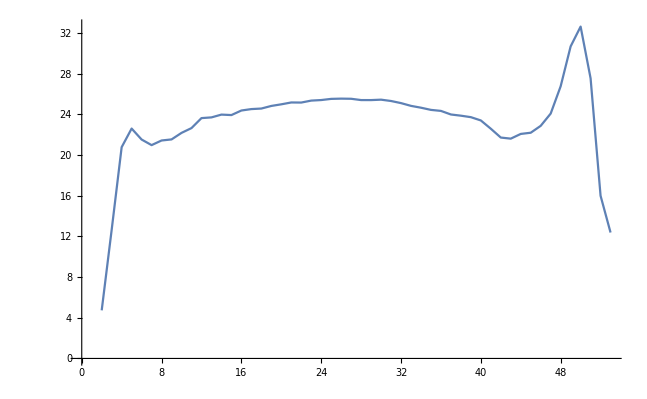
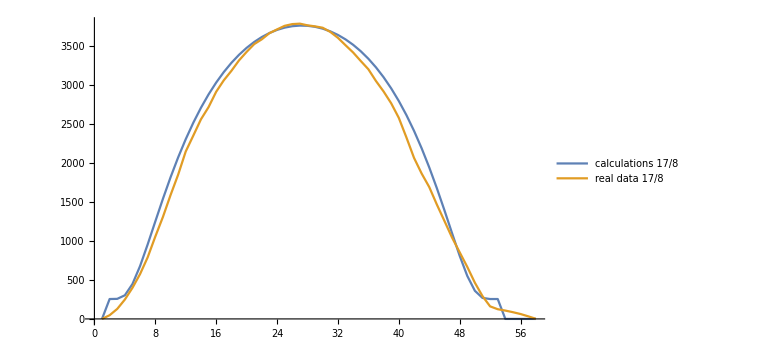
```mathematica
efficiency percentage over 17/8 -Graphics-
-Graphics-
```

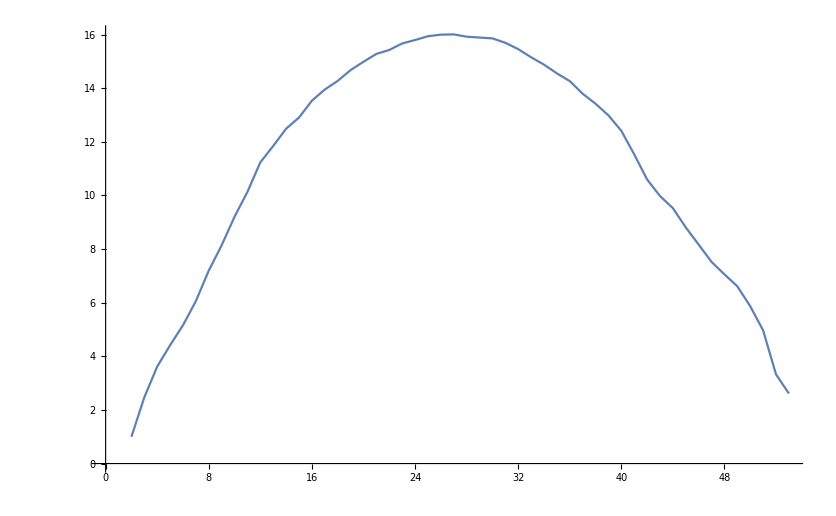
```mathematica
(* Panel efficiency compared to solar irradiation  *)
-Graphics-
```

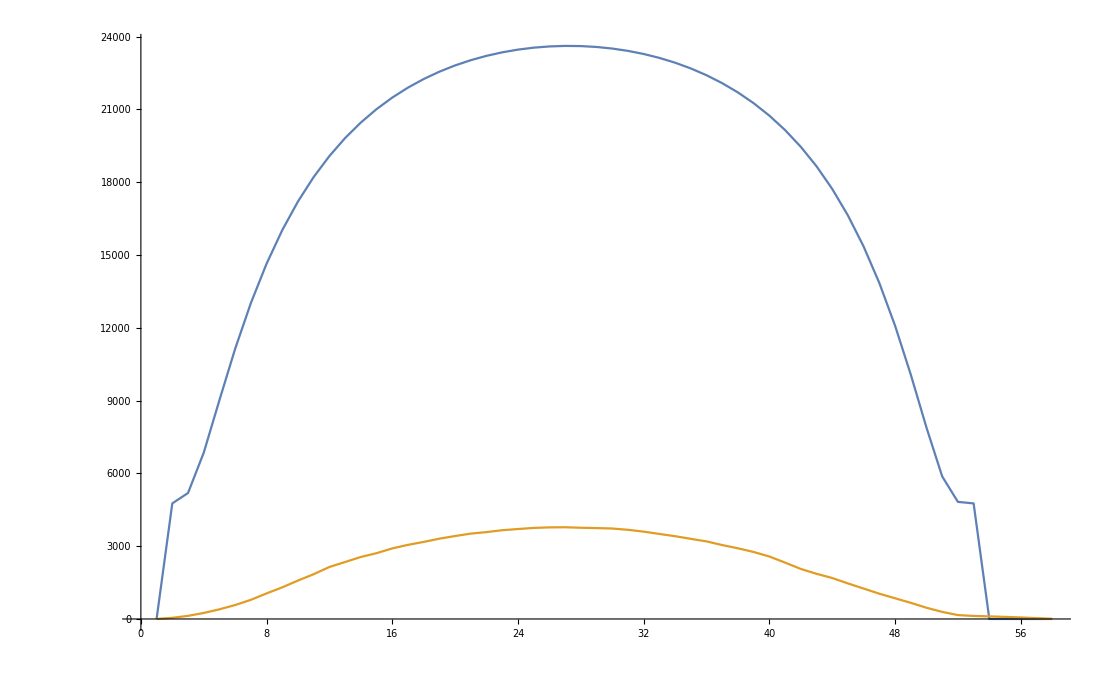
```mathematica
17/8-Graphics-
```

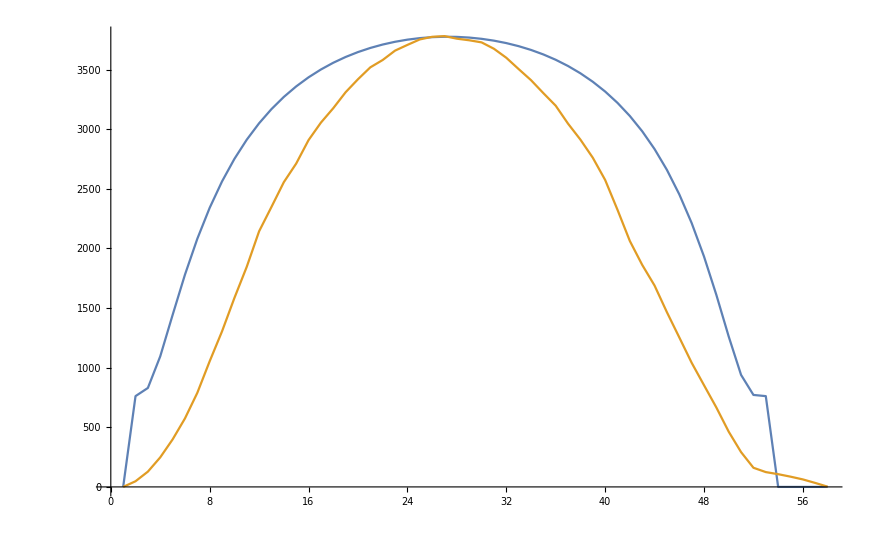
```mathematica
17/8 scaled to 4.22 m2
-Graphics-
```